```mathematica
ClearAll[g,p]
```

```mathematica
l=200;
p=0.09;
d=0.04;
g[l]=(1-d)^150*d;
m=11;
α=0.00272774;
```

```mathematica
g[l-1]=g[l]*(α*(1-3*p)+2*p-(1-d)*(α*(1-3*p)+p)-(1-d)^2*α*p)/(p*(1-α));
g[l-2]=(g[l-1]*(α*(1-3*p)+2*p)-g[l]*(α*(1-3*p)+p+(1-d)*α*p))/(p*(1-α));
For [x=l-3, x>m+1, x-=1,
g[x]=(g[x+1]*(α*(1-3*p)+2*p)-g[x+2]*(α*(1-3*p)+p)-g[x+3]*(α*p))/(p*(1-α));
g[x]=Simplify[g[x]]
]
g[m+1]=
```

```mathematica
Simplify[g[l-2]]
```

(0.0000946605-0.0000727366 α+0.000370536 α^2)/(-1.+α)^2

0.129008

```mathematica
g[14]
```

0.0307471

```mathematica
k[[16]]
```

0.0289682

```mathematica
(1-0.02)^10*0.02
```

0.0163415

```mathematica
dat=Table[{i,(1-0.04)^i*0.04},{i,0,200}];
```

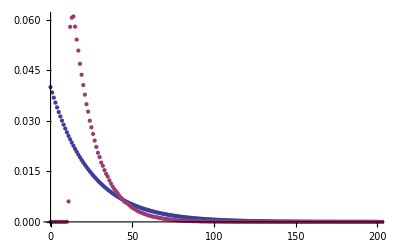

```mathematica
ListPlot[{dat,gapd},PlotRange->{{0,200},Full}]
```

0.86738+List

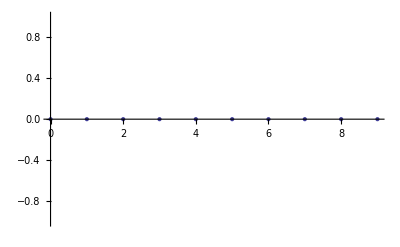

```mathematica
ClearAll[g,p,k];
d=0.02;
m=11;
sum=0;
p=0.09;
l=2/d;
gaps=Table[{i,(1-d)^i*d},{i,0,l}];
g=gaps[[All,2]];
For[i=0,i<l+1,i++,
sum+=g[[i]];]
sum
For[i=0,i<l+1,i++,
g[i]/=sum;]

For[i=0,i<m-1,i++,
k[i]=0;]
k[m-1]=g[m-1]*g[m-1]*(1-3*p)+g[m-1]*p+g[m]*g[m-1]*(1-3*p)+g[m]*p+g[m+1]*g[m-1]*p;
k[m]=-g[m-1]*g[m-1]*(1-3*p)+g[m-1]*(1-2*p)-g[m]*g[m-1]*(1-3*p)+g[m]*(1-2*p)+g[m+1]*g[m-1]*(1-3*p)+g[m+1]*p+g[m+2]*g[m-1]*p;
k[m+1]=-g[m-1]*g[m-1]*p+g[m-1]*p-g[m]*g[m-1]*p+g[m]*p-g[m+1]*g[m-1]*(1-3*p)+g[m+1]*(1-2*p)+g[m+2]*g[m-1]*(1-3*p)+g[m+2]*p+g[m+3]*g[m-1]*p;
For[i=m+2,i<l-1,i++,
k[i]=g[i-1]*(-g[m-1]*p+p)+g[i]*(g[m-1]*(3*p-1)+(1-2*p))+g[i+1]*(g[m-1]*(1-3*p)+p)+g[i+2]*g[m-1]*p;]
For[i=l-1,i<l+1,i++,
k[i]=g[i];]
sum=0;
For[i=0,i<l-1,i++,
sum+=k[i];]
For[i=0,i<l+1,i++,
k[i]/=sum;
g[i]=k[i];]
data=Table[{i,k[i]},{i,0,l-2}];
ListPlot[data,PlotRange->Full]
```

```mathematica
ClearAll[g,p,k];
d=0.02;
m=11;
sum=0;
p=0.09;
l=2/d;
gaps=Table[{i,(1-d)^i*d},{i,0,l}];
g=gaps[[All,2]];
For[i=1,i<l+1,i++,
sum+=g[[i]];]

sum
```

0.86738

```mathematica
g[[99]]
```

0.00276176

```mathematica
g[[0]]
```

List